```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["MaTeX`"];
SetOptions[Charting`ScaledTicks,TicksLength->{.02,.01}];
```

## Decay, scattering and ratio in vacuum

```mathematica
Block[{CS,Cχdec,Cχscat,ratio},Row[{Print["Cχ decay=", Cχdec=(4Pi yχ^2)/(8Pi(2Pi)^3)mϕ^2(1-4 mχ^2/mϕ^2)^(3/2)Assuming[T>0&&mϕ>0,Integrate[√(Eϕ^2-mϕ^2)Exp[-Eϕ/T],{Eϕ,mϕ,Infinity}]]],
Print["Cχ decay expanded = ",Simplify[Cχdec/.mϕ->κ T/.BesselK[1,κ]->1/κ]],

Print["Cχ decay in massless limit = ",Simplify[Normal[Series[Cχdec/.mϕ->κ T/.BesselK[1,κ]->1/κ,{mχ,0,1}]]]],

Print["Cross section = ",CS=(yχ^2yψ^2)/(4Pi s)(1-(4mχ^2)/s)^(3/2)],

Print["Cχscat in massless limit = ",Cχscat=(2Pi^2 T)/(2Pi)^6 Assuming[T>0&&mχ>0&&yψ>0,Integrate[CS s^(3/2) BesselK[1,√s/T],{s,4mχ^2,Infinity}]]//Series[#,{mχ,0,3}]&//Normal//Simplify[#,T>0&&mχ>0]&],

Print["Cχscat/Cχdec = ",ratio=Simplify[Normal[Series[Cχscat/Cχdec/.mϕ->κ T/.BesselK[1,κ]->1/κ,{mχ,0,1}]]]],
 
Print["ratio = ", ratio/.κ->yψ/√6//N]}]]
```

Cχ decay=(mϕ^3 (1-(4 mχ^2)/mϕ^2)^(3/2) T yχ^2 1mϕ/T)/(16 π^3)

Cχ decay expanded = (T^4 yχ^2 (1-(4 mχ^2)/(T^2 κ^2))^(3/2) κ^2)/(16 π^3)

Cχ decay in massless limit = (T^4 yχ^2 κ^2)/(16 π^3)

Cross section = ((1-(4 mχ^2)/s)^(3/2) yχ^2 yψ^2)/(4 π s)

Cχscat in massless limit = (T^4 yχ^2 yψ^2)/(32 π^5)

Cχscat/Cχdec = yψ^2/(2 π^2 κ^2)

ratio = 0.303964

## Scattering with thermal propagator

### setup

```mathematica
gstar=106.75;
entropyS[T_]:=gstar (2Pi^2)/45 T^3;
Hubble[T_]:= 1.66(√gstar)/MPlanck T^2;

MPlanck=1.22 10^(19);

entropytoday=2891.2;

ρch2=1.05 10^(-5);

ReRϕ[T_,yψ_]:=yψ^2/6 T^2; 
kappa[yψ_?NumericQ]:=yψ/(√6);
ImRϕ[s_,yψ_]:=yψ^2/(8Pi)s; 
Γϕ[T_,yψ_]:=yψ^2/(8Pi)√ReRϕ[T,yψ];
```

### scattering rate--Boltzmann

```mathematica
(*factor out yχ^2*)

CSoffTdependent[T_?NumericQ,s_?NumericQ,mχ_?NumericQ,yψ_?NumericQ]:=yψ^2/(4Pi)(1-(4mχ^2)/s)^(3/2)(s (s-ReRϕ[T,yψ])^2)/(((s-ReRϕ[T,yψ])^2+(ReRϕ[T,yψ] yψ^2/(8Pi))^2)^2);

(*define xs=s/T^2 and xχ=mχ/T; factor out yχ^2/T^2: *)
CSoffTindependent[xs_?NumericQ,xχ_?NumericQ,yψ_?NumericQ]:=yψ^2/(4Pi)(1-(4xχ^2)/xs)^(3/2)(xs (xs-yψ^2/6)^2)/(((xs-yψ^2/6)^2+(yψ^2/6 yψ^2/(8Pi))^2)^2) ;
(*factor out yχ^2 T^4: *)


CχscatoffTdependent[T_?NumericQ,mχ_?NumericQ,yψ_?NumericQ]:= (2Pi^2 T)/(2Pi)^6 NIntegrate[CSoffTdependent[T,s,mχ,yψ] s^(3/2) BesselK[1,√s/T],{s, 4mχ^2,Infinity},(*MinRecursion->10,MaxRecursion->20(*Method->{"LocalAdaptive"},*),PrecisionGoal->10,AccuracyGoal->10*)MinRecursion->2,Method->{"LocalAdaptive"},PrecisionGoal->6,AccuracyGoal->6];


CχscatoffTindependent[xχ_?NumericQ,yψ_?NumericQ]:= (2Pi^2)/(2Pi)^6 NIntegrate[CSoffTindependent[xs,xχ,yψ] xs^(3/2) BesselK[1,√xs],{xs, 4xχ^2,Infinity},(*MinRecursion->10,MaxRecursion->20(*Method->{"LocalAdaptive"},*),PrecisionGoal->10,AccuracyGoal->10*)MinRecursion->2,Method->{"LocalAdaptive"},PrecisionGoal->6,AccuracyGoal->6];



(*factor out yχ^2/mχ due to the Planck mass in Hubble. So Yχscatint below is defined as dYscat/dxχ mχ/yχ^2  *)

dYχdxχscat[xχ_?NumericQ,yψ_?NumericQ]:=(*1/mχ*)(2CχscatoffTindependent[xχ,yψ]( 1/xχ)^4)/(entropyS[1/xχ] Hubble[1/xχ] (1/xχ))1/xχ^2; 

Yχscat[mχ_?NumericQ,yψ_?NumericQ]:=NIntegrate[(2CχscatoffTdependent[T,mχ,yψ])/(entropyS[T] Hubble[T] T),{T,0,Infinity},MinRecursion->2,Method->{"LocalAdaptive"},PrecisionGoal->6,AccuracyGoal->6];

ωχscat[mχ_?NumericQ,yψ_?NumericQ]:=Yχscat[mχ,yψ] entropytoday/ρch2 mχ;
```

### scattering rate-quantum statistics

```mathematica
(*define xs=s/T^2 and xχ=mχ/T; factor out yχ^2/T^2: *)
```

```mathematica
CSfull[xs_?NumericQ,xχ_?NumericQ,yψ_?NumericQ]:=yψ^2/(4Pi)(1-(4xχ^2)/xs)^(3/2)(xs (xs-yψ^2/6)^2)/(((xs-yψ^2/6)^2+(yψ^2/6 yψ^2/(8Pi))^2)^2);
CSVacfull[xs_?NumericQ,xχ_?NumericQ,yψ_?NumericQ]:=yψ^2/(4Pi)(1-(4xχ^2)/xs)^(3/2)1/xs;

CχscatVacfull[xχ_?NumericQ,yψ_?NumericQ]:=(2Pi^2)/(2Pi)^6 NIntegrate[CSVacfull[xs,xχ,yψ] xs/2 1/(Exp[(xE1+xE2)/2]+1)1/(Exp[(xE1-xE2)/2]+1)UnitStep[(xE1^2-xs)-xE2^2]UnitStep[xE1-√xs],{xE2,-Infinity,Infinity},{xE1,0,Infinity},{xs,4xχ^2,Infinity},MinRecursion->10,MaxRecursion->20,PrecisionGoal->10,AccuracyGoal->10];

(*factor out yχ^2 T^4: *)
Cχscatfull[xχ_?NumericQ,yψ_?NumericQ]:=(2Pi^2)/(2Pi)^6 NIntegrate[CSfull[xs,xχ,yψ] xs/2 1/(Exp[(xE1+xE2)/2]+1)1/(Exp[(xE1-xE2)/2]+1)UnitStep[(xE1^2-xs)-xE2^2]UnitStep[xE1-√xs],{xE2,-Infinity,Infinity},{xE1,0,Infinity},{xs,4xχ^2,Infinity},MinRecursion->2,Method->{"LocalAdaptive"},PrecisionGoal->6,AccuracyGoal->6];

Yχscatfull[mχ_?NumericQ,yψ_?NumericQ]:=2(2Pi^2)/(2Pi)^6 NIntegrate[ CSfull[xs,xχ,yψ] xs/2 1/(Exp[(xE1+xE2)/2]+1)1/(Exp[(xE1-xE2)/2]+1)UnitStep[(xE1^2-xs)-xE2^2]UnitStep[xE1-√xs]UnitStep[xs-4xχ^2](mχ/xχ)^4/(entropyS[mχ/xχ] Hubble[mχ/xχ] mχ/xχ)mχ/xχ^2,{xE2,-Infinity,Infinity},{xE1,0,Infinity},{xs,0,Infinity}, {xχ,0,Infinity},MinRecursion->2,Method->{"LocalAdaptive"},PrecisionGoal->6,AccuracyGoal->6];
ωχscatfull[mχ_?NumericQ,yψ_?NumericQ]:=Yχscatfull[mχ,yψ] entropytoday/ρch2 mχ;
```

### decay rate-Boltzmann

```mathematica
Clear[dYχdxχdec]
```

```mathematica
mϕT[T_,yψ_]:=√ReRϕ[T,yψ];

Tc[mχ_,yψ_]:=2mχ/(yψ/√6);

Cχdec[T_,mχ_,yψ_]:=1/(16Pi^3)mϕT[T,yψ]^3(1-(4mχ^2)/mϕT[T,yψ]^2)^(3/2)T BesselK[1,mϕT[T,yψ]/T];
(* factor out yχ^2 T^4:  *)
CχdecTindependent[xχ_,yψ_]:=Cχdec[T,mχ,yψ]/T^4/.mχ->T xχ//Simplify[#,T>0]&;

Yχdec[mχ_?NumericQ,yψ_?NumericQ]:= Assuming[mχ>0&&yψ>0,NIntegrate[(2Cχdec[T,mχ,yψ])/(entropyS[T] Hubble[T] T) , {T,Tc[mχ,yψ],Infinity},MinRecursion->2]];

(*factor out yχ^2/mχ due to the Planck mass in Hubble. So dYχdxχdec below is defined as dYdec/dxχ mχ/yχ^2   *)

dYχdxχdec[xχ_,yψ_?NumericQ]:=(*1/mχ*)(2CχdecTindependent[xχ,yψ]( 1/xχ)^4)/(entropyS[1/xχ] Hubble[1/xχ] (1/xχ))1/xχ^2; 

YχdecTR[TR_?NumericQ,mχ_?NumericQ,yψ_?NumericQ]:=If[TR>Tc[mχ,yψ],Assuming[mχ>0&&yψ>0,NIntegrate[(2Cχdec[T,mχ,yψ])/(entropyS[T] Hubble[T] T), {T,Tc[mχ,yψ],TR},MinRecursion->2]],0];

ωχdec[mχ_?NumericQ,yψ_?NumericQ]:=Yχdec[mχ,yψ] entropytoday/ρch2 mχ;


ωχdecTR[TR_?NumericQ,mχ_?NumericQ,yψ_?NumericQ]:=YχdecTR[TR,mχ,yψ] entropytoday/ρch2 mχ;

yχdecFit[mχ_?NumericQ,yψ_?NumericQ]:=√(0.12/ωχdec[mχ,yψ]);

yχdecFitTR[TR_?NumericQ,mχ_?NumericQ,yψ_?NumericQ]:=If[TR>Tc[mχ,yψ],√(0.12/ωχdecTR[TR,mχ,yψ]),0];
```

### decay rate-quantum statistics

```mathematica
(* factor out yχ^2 T^4:  *)
```

```mathematica
Cχdecfull[xχ_?NumericQ,yψ_?NumericQ]:=(*T^4*)(4Pi (*yχ^2*))/(8Pi(2Pi)^3)kappa[yψ]^2(1-4 xχ^2/kappa[yψ]^2)^(3/2)NIntegrate[√(xE^2-kappa[yψ]^2)1/(Exp[xE]-1),{xE,kappa[yψ],Infinity}]; 

Yχdecfull[mχ_?NumericQ,yψ_?NumericQ]:= NIntegrate[(2Cχdecfull[xχ,yψ] (mχ/xχ)^4)/(entropyS[mχ/xχ] Hubble[mχ/xχ] mχ/xχ) mχ/xχ^2, {xχ,0,kappa[yψ]/2},MinRecursion->3];
ωχdecfull[mχ_?NumericQ,yψ_?NumericQ]:=Yχdecfull[mχ,yψ] entropytoday/ρch2 mχ;
```

### scat/decay ratio: collision rate

#### Ratio with Boltzmann distribution and vacuum scattering

```mathematica
CχdecVacBoltzmann=(4Pi yχ^2)/(8Pi(2Pi)^3)mϕ^2(1-4 mχ^2/mϕ^2)^(3/2)Assuming[T>0&&mϕ>0,Integrate[√(Eϕ^2-mϕ^2)Exp[-Eϕ/T],{Eϕ,mϕ,Infinity}]];
CχscatVacBoltzmann=(2Pi^2 T)/(2Pi)^6 Assuming[T>0&&mχ>0&&yψ>0,Integrate[(yχ^2yψ^2)/(4Pi s)(1-(4mχ^2)/s)^(3/2)  s^(3/2) BesselK[1,√s/T],{s,4mχ^2,Infinity}]]//Series[#,{mχ,0,3}]&//Normal//Simplify[#,T>0&&mχ>0]&;
RVacBoltzmann=Simplify[Normal[Series[CχscatVacBoltzmann/CχdecVacBoltzmann/.mϕ->κ T/.BesselK[1,κ]->1/κ,{mχ,0,1}]]]/.κ->yψ/√6//N
```

0.303964

#### Ratio with full distribution and vacuum scattering

```mathematica
RVacFD=Do[Print["γ_scat/γ_dec=",CχscatVacfull[10^-8,10^(-(5-i))]/Cχdecfull[10^-8,10^(-(5-i))]],{i,4}]
```

γ_scat/γ_dec=0.125008

γ_scat/γ_dec=0.12505

γ_scat/γ_dec=0.125487

γ_scat/γ_dec=0.129877

#### Ratio with Boltzmann distribution and thermally corrected scattering

```mathematica
RTBoltzmann=Do[Print["γ_scat/γ_dec=",CχscatoffTindependent[10^-8,10^(-(5-i))]/CχdecTindependent[10^-8,10^(-(5-i))]],{i,4}]
```

γ_scat/γ_dec=0.303321

γ_scat/γ_dec=0.303321

γ_scat/γ_dec=0.303843

γ_scat/γ_dec=0.806486

#### Ratio with full and thermally corrected scattering

```mathematica
RTFD=Do[Print["γ_scat/γ_dec=",Cχscatfull[10^-8,10^(-(5-i))]/Cχdecfull[10^-8,10^(-(5-i))]],{i,4}]
```

γ_scat/γ_dec=0.124974

γ_scat/γ_dec=0.12502

γ_scat/γ_dec=0.125463

γ_scat/γ_dec=0.13052

### scat v.s. decay--Boltzmann: plot

```mathematica
ScatDecPlot=LogLogPlot[{CχdecTindependent[xχ,0.1],CχscatoffTindependent[xχ,0.1],CχdecTindependent[xχ,0.01],CχscatoffTindependent[xχ,0.01],CχdecTindependent[xχ,0.001],CχscatoffTindependent[xχ,0.001],CχdecTindependent[xχ,0.0001],CχscatoffTindependent[xχ,0.0001]},{xχ,10^(-6),3},PlotRange->{{10^(-6),3},{10^-16,10^-4}},PlotStyle->{Directive[Darker@Green,Thickness[0.005]],Directive[Darker@Green,Dashing[Medium], Thickness[0.005]],Directive[RGBColor[0.3,0.56,1.],Thickness[0.005]],Directive[RGBColor[0.3,0.56,1.],Dashing[Medium], Thickness[0.005]],
Directive[Darker@Red,Thickness[0.005]],Directive[Darker@Red,Dashing[Medium],Thickness[0.005]],Directive[RGBColor[0.83,0.32,1.],Thickness[0.005]],Directive[RGBColor[0.83,0.32,1.],Dashing[Medium], Thickness[0.005]]},
GridLines->{{0.1/(2 √6),0.01/(2 √6),0.001/(2 √6),0.0001/(2 √6),(*xχ= *)√(1/4)},{}},GridLinesStyle->Directive[Black,Thickness[0.001],Dotted],
Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{MaTeX["\\boldsymbol{x_\\chi\\equiv m_\\chi/T}",FontSize->20],MaTeX["\\boldsymbol{\\gamma\\times y_\\chi^{-2}\\times T^{-4}}",FontSize->20]},
FrameTicksStyle->Directive[Black,Thickness[0.005],18],ImageSize->500,AspectRatio->0.75,Epilog->{Inset[LineLegend[{Directive[Black,Dashing[Medium]],Directive[Black]},{MaTeX["\\boldsymbol{\\textbf{scattering}}",FontSize->17],
MaTeX["\\boldsymbol{\\textbf{forbidden~decay}}",FontSize->17]},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Gray]&),LegendMargins->3,LegendLayout->{"Row",2}],Scaled[{0.75,0.16}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-1}}",FontSize->17]],0Degree],Scaled[{0.15,0.92}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-2}}",FontSize->17]],0Degree],Scaled[{0.15,0.76}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-3}}",FontSize->17]],0Degree],Scaled[{0.15,0.6}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-4}}",FontSize->17]],0Degree],Scaled[{0.15,0.42}]]
}]
```

-Graphics-

```mathematica
Export["collisionrate.pdf",Style[ScatDecPlot,Background->None]];
(*SystemOpen[DirectoryName[AbsoluteFileName["collisionrate.pdf"]]]*)
```

### scat vs decay: relic density--Boltzmann+full quantum statistics

#### relic density ratio--Fit

```mathematica
OmegaRatio=ParallelTable[{yψ//N,ωχscat[1,yψ]/ωχdec[1,yψ]//N},{yψ,{10^(-5),(*3 10^(-5),*)5 10^(-5),(*7 10^(-5),*)1 10^(-4),5 10^(-4),(*6 10^(-4),9 10^(-4),*)1 10^(-3),5 10^(-3),(*7 10^(-3),9 10^(-3),*)0.01,(*0.02,0.03,*)0.05,(*0.06,0.08,*)0.1,(*0.2,0.3,0.4,*)0.5,(*0.6,0.7,0.8,0.9,*)1}}]
```

(0.00001 | 145705.
0.00005 | 31690.4
0.0001 | 17039.4
0.0005 | 3533.73
0.001 | 1759.39
0.005 | 351.052
0.01 | 175.931
0.05 | 35.631
0.1 | 18.1183
0.5 | 4.27506
1. | 2.6975)

```mathematica
OmegaRatioFull=ParallelTable[{yψ//N,ωχscatfull[1,yψ]/ωχdecfull[1,yψ]//N},{yψ,{10^(-5),(*3 10^(-5),*)5 10^(-5),(*7 10^(-5),*)1 10^(-4),5 10^(-4),(*6 10^(-4),9 10^(-4),*)1 10^(-3),5 10^(-3),(*7 10^(-3),9 10^(-3),*)0.01,(*0.02,0.03,*)0.05,(*0.06,0.08,*)0.1,(*0.2,0.3,0.4,*)0.5,(*0.6,0.7,0.8,0.9,*)1}}]
```

(0.00001 | 80204.9
0.00005 | 16041.1
0.0001 | 8020.66
0.0005 | 1604.41
0.001 | 802.36
0.005 | 160.722
0.01 | 80.5176
0.05 | 16.3567
0.1 | 8.34125
0.5 | 2.08561
1. | 1.42854)

```mathematica
Table[{OmegaRatio[[i,2]]/OmegaRatioFull[[i,2]]},{i,1,Length[OmegaRatio]}]
```

(1.81666
1.97557
2.12444
2.20252
2.19277
2.18422
2.185
2.17837
2.17213
2.04979
1.88829)

```mathematica
OmegaRatioFit=0.8 yψ+1.8/yψ+0.5;
OmegaRatioFullFit=OmegaRatioFit/2.0;
```

#### relic density ratio--plot

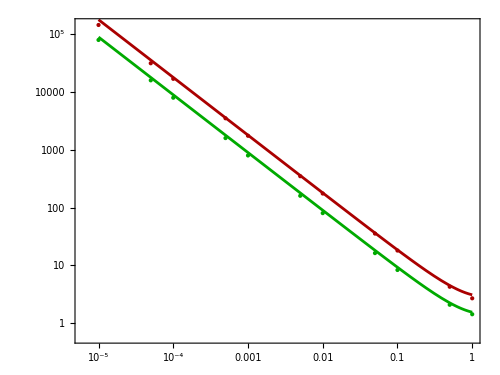

```mathematica
OmegaRatioPlot=Show[ListLogLogPlot[{OmegaRatio,OmegaRatioFull},PlotRange->All,PlotStyle->{Directive[Darker@Red,PointSize[Large]],Directive[Darker@Green,PointSize[Large]]}],LogLogPlot[{OmegaRatioFit,OmegaRatioFullFit},{yψ,10^(-5),1},PlotStyle->{Directive[Darker@Red,Thickness[0.004]],Directive[Darker@Green,Thickness@0.004]}],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{MaTeX["\\boldsymbol{\\textbf{thermal~coupling}~y_\\psi}",FontSize->20],MaTeX["\\boldsymbol{\\Omega_{2\\psi\\to2\\chi,\\rm off }/\\Omega_{\\phi\\to 2\\chi}}",FontSize->20]},
FrameTicksStyle->Directive[Black,Thickness[0.005],18],ImageSize->500,AspectRatio->0.75,Epilog->{Inset[LineLegend[{Directive[Darker@Red],Directive[Darker@Green]},{MaTeX["\\boldsymbol{\\textbf{Boltzmann~Statistics}}",FontSize->17],
MaTeX["\\boldsymbol{\\textbf{Quantum Statistics}}",FontSize->17]},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Gray]&),LegendMargins->3,LegendLayout->{"Row",2}],Scaled[{0.72,0.85}]]}]
```

```mathematica
Export["OmegaR.pdf",Style[OmegaRatioPlot,Background->None]];
SystemOpen[DirectoryName[AbsoluteFileName["OmegaR.pdf"]]]
```

#### relic density--coupling correlation plot

```mathematica
ωχtot[yχ_?NumericQ,yψ0_?NumericQ]:=yχ^2(1+OmegaRatioFit/.yψ->yψ0)ωχdec[1,yψ0];
ωχFulltot[yχ_?NumericQ,yψ0_?NumericQ]:=yχ^2(1+OmegaRatioFullFit/.yψ->yψ0)ωχdecfull[1,yψ0];
```

```mathematica
{ωχdec[1,0.1]/ωχtot[1,0.1],ωχdec[1,1]/ωχtot[1,1],ωχdecfull[1,0.1]/ωχFulltot[1,0.1],ωχdecfull[1,1]/ωχFulltot[1,1]}
```

{0.0510725,0.243902,0.0971817,0.392157}

```mathematica
Omegatot=ContourPlot[{ωχtot[yχ,yψ]==0.12,yχ^2 ωχdec[1,yψ]==0.12},{yψ,10^(-5),1},{yχ,5 10^-12,2 10^-4},ContourStyle->{Directive[RGBColor[1.,0.2,0.3],Thickness[0.005]],Directive[RGBColor[0.,0.15,0.7],Thickness@0.005]},ScalingFunctions->{"Log","Log"},Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],FrameLabel->{MaTeX["\\boldsymbol{\\textbf{thermal~coupling}~y_\\psi}",FontSize->20],MaTeX["\\boldsymbol{\\textbf{DM~coupling}~y_\\chi}",FontSize->20]},
FrameTicksStyle->Directive[Black,Thickness[0.005],18],ImageSize->500,AspectRatio->0.75];
```

```mathematica
Omegafulltot=ContourPlot[{ωχFulltot[yχ,yψ]==0.12,yχ^2 ωχdecfull[1,yψ]==0.12},{yψ,10^(-5),1},{yχ,5 10^-12,2 10^-4},ContourStyle->{Directive[RGBColor[1.,0.2,0.3],Thickness[0.005],Dashing[Large]],Directive[RGBColor[0.,0.15,0.7],Thickness@0.005,,Dashing[Large]]},ScalingFunctions->{"Log","Log"},Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{MaTeX["\\boldsymbol{\\textbf{thermal~coupling}~y_\\psi}",FontSize->20],MaTeX["\\boldsymbol{\\textbf{DM~coupling}~y_\\chi}",FontSize->20]},
FrameTicksStyle->Directive[Black,Thickness[0.005],18],ImageSize->500,AspectRatio->0.75];
```

```mathematica
Omegashow=Show[Omegatot,Omegafulltot,Epilog->{
Inset[Rotate[Style[MaTeX["\\boldsymbol{\\Omega_{\\rm scat+decay}=\\Omega_{\\rm obs}}",FontSize->17]],-26Degree],Scaled[{0.45,0.48}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{\\Omega_{\\rm decay}=\\Omega_{\\rm obs}}",FontSize->17]],-35Degree],Scaled[{0.5,0.62}]],
Inset[LineLegend[{Directive[Black],
Directive[Black,Dashing[Large]]},{MaTeX["\\boldsymbol{\\textbf{Boltzmann~Statistics}}",FontSize->15],
MaTeX["\\boldsymbol{\\textbf{Quantum~Statistics}}",FontSize->15]},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Gray]&),LegendMargins->3,LegendLayout->{"Row",2}],Scaled[{0.72,0.85}]]}]
```

-Graphics-

```mathematica
Export["couplingco.pdf",Style[Omegashow,Background->None]];
(*SystemOpen[DirectoryName[AbsoluteFileName["couplingco.pdf"]]]*)
```

## Eq. of Y(T)

```mathematica
(*YTdecfun=yψ^2/mχ dY/dxχ *)
```

```mathematica
xχmin=1.0 10^-8;

YTdecfun[yψ_?NumericQ]:=NDSolve[{Y1'[xχ]==dYχdxχdec[xχ,yψ],Y1[xχmin]==0},Y1,{xχ,xχmin,5}];

YTscatfun[yψ_?NumericQ]:=NDSolve[{Y2'[xχ]==dYχdxχscat[xχ,yψ],Y2[xχmin]==0},Y2,{xχ,xχmin,5}];


Ydecoft[yψ_?NumericQ,xχ0_]:=(Y1[xχ]/.YTdecfun[yψ])[[1]]/.{xχ-> xχ0};


Yscatoft[yψ_?NumericQ,xχ0_]:=(Y2[xχ]/.YTscatfun[yψ])[[1]]/.{xχ-> xχ0};
```

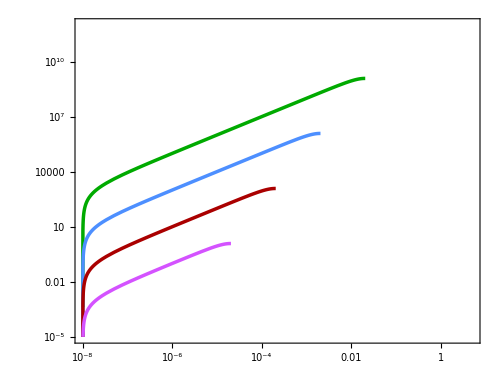

```mathematica
YofTdecplot=LogLogPlot[{Evaluate[Ydecoft[0.1,xχ]],(*Evaluate[Yscatoft[0.1,xχ]],*)Evaluate[Ydecoft[0.01,xχ]],(*Evaluate[Yscatoft[0.01,xχ]],*)Evaluate[Ydecoft[0.001,xχ]],(*Evaluate[Yscatoft[0.001,xχ]],*)Evaluate[Ydecoft[0.0001,xχ]](*Evaluate[Yscatoft[0.0001,xχ]]*)},{xχ,10^(-8),5},PlotRange->{{10^(-8),5},{10^-5,10^12}},PlotStyle->{Directive[Darker@Green,Thickness[0.005]],Directive[RGBColor[0.3,0.56,1.],Thickness[0.005]],
Directive[Darker@Red,Thickness[0.005]],Directive[RGBColor[0.83,0.32,1.],Thickness[0.005]]},
GridLines->{{0.1/(2 √6),0.01/(2 √6),0.001/(2 √6),0.0001/(2 √6),(*xχ= *)√(1/4)},{}},GridLinesStyle->Directive[Black,Thickness[0.001],Dotted],
Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{MaTeX["\\boldsymbol{x_\\chi\\equiv m_\\chi/T}",FontSize->20],MaTeX["\\boldsymbol{Y_\\chi(T) \\times m_\\chi\\times y_\\chi^{-2} ~[\\textbf{GeV}]}",FontSize->20]},
FrameTicksStyle->Directive[Black,Thickness[0.005],18],ImageSize->500,AspectRatio->0.75]
```

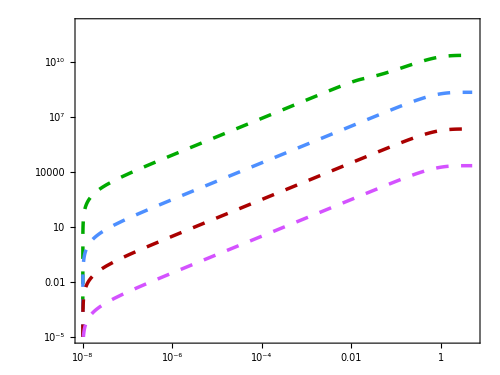

```mathematica
YofTscatplot=LogLogPlot[{Evaluate[Yscatoft[0.1,xχ]],Evaluate[Yscatoft[0.01,xχ]],Evaluate[Yscatoft[0.001,xχ]],Evaluate[Yscatoft[0.0001,xχ]]},{xχ,10^(-8),5},PlotRange->{{10^(-8),5},{10^-5,10^12}},PlotStyle->{Directive[Darker@Green,Dashing[Medium], Thickness[0.005]],Directive[RGBColor[0.3,0.56,1.],Dashing[Medium], Thickness[0.005]],
Directive[Darker@Red,Dashing[Medium],Thickness[0.005]],Directive[RGBColor[0.83,0.32,1.],Dashing[Medium], Thickness[0.005]]},
GridLines->{{0.1/(2 √6),0.01/(2 √6),0.001/(2 √6),0.0001/(2 √6),(*xχ= *)√(1/4)},{}},GridLinesStyle->Directive[Black,Thickness[0.001],Dotted],
Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{MaTeX["\\boldsymbol{x_\\chi\\equiv m_\\chi/T}",FontSize->20],MaTeX["\\boldsymbol{Y_\\chi(T) \\times m_\\chi\\times y_\\chi^{-2} ~[\\textbf{GeV}]}",FontSize->20]},
FrameTicksStyle->Directive[Black,Thickness[0.005],18],ImageSize->500,AspectRatio->0.75]
```

```mathematica
YofTplotre=Show[YofTdecplot,YofTscatplot,FrameLabel->{MaTeX["\\boldsymbol{x_\\chi\\equiv m_\\chi/T}",FontSize->20],MaTeX["\\boldsymbol{Y_\\chi \\times m_\\chi\\times y_\\chi^{-2} ~[\\textbf{GeV}]}",FontSize->20]},Epilog->{Inset[LineLegend[{Directive[Black,Dashing[Medium]],Directive[Black]},{MaTeX["\\boldsymbol{\\textbf{scattering}}",FontSize->17],
MaTeX["\\boldsymbol{\\textbf{forbidden~decay}}",FontSize->17]},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Gray]&),LegendMargins->3,LegendLayout->{"Row",2}],Scaled[{0.75,0.14}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-1}}",FontSize->17]],20Degree],Scaled[{0.15,0.58}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-2}}",FontSize->17]],20Degree],Scaled[{0.15,0.46}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-3}}",FontSize->17]],20Degree],Scaled[{0.15,0.34}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-4}}",FontSize->17]],20Degree],Scaled[{0.15,0.22}]]
}]
```

-Graphics-

```mathematica
Export["YchiofT.pdf",Style[YofTplotre,Background->None]];
```